## Standard Ricker model EWS

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-0.2;
bh=1;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="trans_r_long";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[dfKtau]-1
```

100

```mathematica
(* Realisation number to display *)
displayNum=3;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
```

```mathematica
(* Extract info of one trajectory *)
trajVals=Cases[dfEws[[2;;,{1,3,4}]],{displayNum,_,_}][[;;,{2,3}]];
tVals = trajVals[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
```

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[trajVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
AxesLabel->{"t","x(t)"},
PlotRange->{{0,tmax},All}];
```

### Plot format adjustment

```mathematica
rTicks=Round[Range[bh,bl,-0.2],0.1];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

```mathematica
rTicks
```

{1.,0.8,0.6,0.4,0.2,0.,-0.2}

```mathematica
plotTraj=Show[plotX,
PlotRange->{{0,tmax},{0,170}},
ImageSize->imgs,
LabelStyle->ls,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Growth rate, r"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Arrowheads[{-aHeadSize,aHeadSize}*0.7],
Thickness[0.002],
Arrow[{Scaled[{0,0.2},{0,0}],Scaled[{0,0.2},{windowComps*dt2,0}]}]
}
];
```

## EWS Plots

### Variance

```mathematica
(* plot colour *)
colVar=TMBcolours[[2]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
varEws=Table[Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims}];
```

```mathematica
varEws//Dimensions
```

{100}

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotVar=ListLinePlot[varEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}];
```

### Coefficient of variation

```mathematica
(* plot colour *)
colCV=TMBcolours[[3]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
cvEws=Table[Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotCv=ListLinePlot[cvEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colCV,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}];
```

### Smax/Mean

```mathematica
(* plot colour *)
colSmaxMean=TMBcolours[[4]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Mean"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxMeanEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxMean=ListPlot[smaxMeanEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxMean,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/<X>",ls],textPos,{-1,0}]}];
```

### Smax/Var

```mathematica
(* plot colour *)
colSmaxVar=TMBcolours[[5]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxVarEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSmaxVar=ListPlot[smaxVarEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["S_max/Variance",ls],textPos,{-1,0}]}];
```

### Skewness

```mathematica
(* plot colour *)
colSkew=TMBcolours[[5]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
(* Construct relevant sub dataframe *)
smaxVarEws=Table[DeleteCases[
Cases[dfEws[[2;;,{1,3,indexEws}]],{realNum,_,_}][[;;,{2,3}]],
{_,""}]
,{realNum,1,numSims}];
```

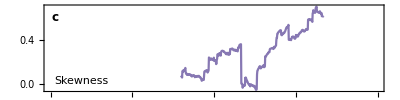

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotSkew=ListPlot[smaxVarEws[[1]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
PlotStyle->colSmaxVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Autocorrelation (combined)

```mathematica
(* plot colour *)
colAC=TMBcolours[[{4,5,7}]];
```

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
```

```mathematica
(* Construct relevant sub dataframe *)
acEws=Table[Cases[dfEws[[2;;,{1,3,indexEws[[i]]}]],{realNum,_,_}][[;;,{2,3}]],{realNum,1,numSims},{i,1,3}];
```

```mathematica
acEws//Dimensions
```

{100,3}

```mathematica
(* line legend *)
legend=LineLegend[colAC,Table["lag-"<>ToString[i],{i,{1,2,3}}],Spacings->{0,0.2},LabelStyle->(ls-1)]
```

```mathematica
(* Plot variance EWS for display param *)
ymin=-0.02;
ymax=0.3;
plotAC=ListLinePlot[acEws[[displayNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
PlotRange->{{0,tmax},All},
PlotStyle->colAC,
Axes->False,
PlotLegends->Placed[legend,{0.15,0.65}],
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Autocorrelation",ls],textPos,{-1,0}]}];
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

```mathematica
stateVals={"x"};
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

5

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | -0.990552 | -0.987557 | -0.984667 | -0.98821 | -0.988506 | -0.991775 | -0.981377 | -0.979753 | -0.989265 | -0.992682 | -0.990193 | -0.985574 | -0.991669 | -0.98916 | -0.991627 | -0.990298 | -0.984709 | -0.992787 | -0.992386 | -0.98916 | -0.990045 | -0.990552 | -0.98627 | -0.989581 | -0.989434 | -0.993504 | -0.992829 | -0.992534 | -0.990214 | -0.984709 | -0.986945 | -0.988653 | -0.98665 | -0.989961 | -0.986734 | -0.99304 | -0.988674 | -0.991374 | -0.987198 | -0.990172 | -0.981694 | -0.987768 | -0.989856 | -0.987915 | -0.991775 | -0.992049 | -0.993736 | -0.99188 | -0.986629 | -0.989138 | -0.993251 | -0.988611 | -0.989834 | -0.987177 | -0.989054 | -0.991669 | -0.981588 | -0.992534 | -0.99285 | -0.990762 | -0.986544 | -0.987852 | -0.98608 | -0.987873 | -0.977855 | -0.983528 | -0.992302 | -0.991943 | -0.97872 | -0.981335 | -0.993989 | -0.990741 | -0.987051 | -0.991754 | -0.985068 | -0.980344 | -0.983908 | -0.986608 | -0.989117 | -0.985173 | -0.993799 | -0.989792 | -0.992197 | -0.991564 | -0.988738 | -0.989961 | -0.992703 | -0.989033 | -0.982959 | -0.990805 | -0.987789 | -0.993019 | -0.976885 | -0.989708 | -0.986565 | -0.988801 | -0.988696 | -0.978867 | -0.987957 | -0.99072

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colVar,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.606749 | 0.856185 | 0.767732 | 0.248677 | 0.276474 | 0.0778867 | 0.64739 | 0.827818 | 0.550754 | 0.426722 | 0.437077 | 0.000210904 | 0.636086 | 0.869303 | 0.352272 | 0.362881 | 0.360181 | -0.419045 | 0.741073 | 0.618813 | 0.268312 | 0.233871 | 0.491258 | 0.272572 | 0.771992 | 0.192829 | 0.511547 | -0.413308 | 0.409659 | 0.591037 | 0.35668 | 0.107519 | 0.348835 | 0.635326 | -0.356512 | 0.262259 | -0.325804 | 0.671539 | -0.228261 | 0.283412 | 0.469851 | 0.239798 | 0.28917 | 0.537066 | 0.587936 | 0.214616 | -0.0646631 | 0.0932405 | -0.310851 | 0.278604 | -0.375324 | 0.0473901 | 0.514141 | 0.748877 | 0.727765 | -0.00862596 | 0.6236 | -0.0598967 | 0.133418 | -0.0141095 | 0.708067 | 0.596162 | 0.692376 | 0.595023 | 0.45049 | 0.683202 | 0.42069 | 0.405694 | 0.839102 | 0.677465 | 0.315027 | 0.0137509 | -0.60542 | 0.523906 | -0.306 | -0.305494 | 0.561805 | 0.602995 | 0.537594 | 0.666308 | -0.255974 | 0.233955 | 0.422757 | 0.151935 | -0.318908 | 0.771655 | 0.540209 | 0.470589 | -0.233977 | 0.342972 | -0.232817 | 0.588738 | 0.429379 | 0.0503216 | 0.265697 | 0.835284 | 0.511884 | 0.834968 | 0.510999 | 0.696151

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[{#,#,#}&@Flatten[ktauVals[[;;,2;;]]],
If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colSkew,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

10

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.832289 | 0.976864 | 0.916714 | 0.946114 | 0.961341 | 0.924307 | 0.872656 | 0.942318 | 0.903891 | 0.79517 | 0.759401 | 0.95668 | 0.899779 | 0.940799 | 0.873648 | 0.843193 | 0.925551 | 0.934599 | 0.924539 | 0.932933 | 0.900243 | 0.641611 | 0.920384 | 0.961742 | 0.94875 | 0.593125 | 0.920932 | 0.888495 | 0.901192 | 0.965834 | 0.919477 | 0.831952 | 0.897627 | 0.890035 | 0.918022 | 0.885163 | 0.901613 | 0.913213 | 0.924412 | 0.843615 | 0.910598 | 0.939618 | 0.902499 | 0.941432 | 0.960624 | 0.760603 | 0.909122 | 0.907772 | 0.922493 | 0.803058 | 0.898555 | 0.808816 | 0.89303 | 0.949299 | 0.953264 | 0.91625 | 0.959907 | 0.877275 | 0.780597 | 0.878773 | 0.919561 | 0.903891 | 0.966972 | 0.967436 | 0.798988 | 0.974966 | 0.920679 | 0.923927 | 0.91876 | 0.937826 | 0.839439 | 0.842603 | 0.959148 | 0.893304 | 0.719857 | 0.955014 | 0.918549 | 0.926289 | 0.947801 | 0.875883 | 0.901044 | 0.890393 | 0.890436 | 0.695666 | 0.913719 | 0.936919 | 0.955436 | 0.747844 | 0.94158 | 0.897459 | 0.948877 | 0.815733 | 0.958579 | 0.742866 | 0.920152 | 0.877507 | 0.913403 | 0.967837 | 0.943921 | 0.934325

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[{#,#,#}&@Flatten[ktauVals[[;;,2;;]]],
If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colCV,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | -0.930736 | -0.65368 | -0.87013 | -0.445887 | -0.809524 | -0.731602 | -0.454545 | -0.705628 | -0.549784 | -0.82684 | -0.688312 | -0.800866 | -0.748918 | -0.896104 | -0.939394 | -0.809524 | -0.904762 | -0.95671 | -0.887446 | -0.549784 | -0.809524 | -0.87013 | -0.766234 | -0.705628 | -0.705628 | -0.948052 | -0.800866 | -0.844156 | -0.748918 | -0.411255 | -0.835498 | -0.930736 | -0.87013 | -0.91342 | -0.948052 | -0.930736 | -0.852814 | -0.896104 | -0.887446 | -0.670996 | -0.489177 | -0.359307 | -0.861472 | -0.887446 | -0.662338 | -0.887446 | -0.87013 | -0.670996 | -0.722944 | -0.91342 | -0.974026 | -0.774892 | -0.965368 | -0.558442 | -0.575758 | -0.818182 | -0.584416 | -0.835498 | -0.844156 | -0.515152 | -0.757576 | -0.922078 | -0.0995671 | -0.177489 | -0.670996 | -0.367965 | -0.896104 | -0.506494 | 0.220779 | -0.705628 | -0.774892 | -0.645022 | -0.52381 | -0.878788 | -0.861472 | -0.705628 | -0.5671 | -0.887446 | -0.878788 | -0.809524 | -0.766234 | -0.861472 | -0.887446 | -0.930736 | -0.645022 | -0.835498 | -0.69697 | -0.766234 | -0.731602 | -0.844156 | -0.87013 | -0.896104 | -0.82684 | -0.748918 | -0.627706 | -0.887446 | -0.965368 | -0.844156 | -0.69697 | -0.160173

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[{ktauVals[[;;,2;;]],ktauVals[[;;,2;;]],ktauVals[[;;,2;;]]},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{{Opacity[1]},{Opacity[0.5]},{Opacity[0]}},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

11

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

x | 0.835498 | 0.878788 | 0.948052 | 0.844156 | 0.948052 | 0.74026 | 0.878788 | 0.774892 | 0.844156 | 0.904762 | 0.575758 | 0.91342 | 0.939394 | 0.904762 | 0.69697 | 0.922078 | 0.506494 | 0.350649 | 0.844156 | 0.91342 | 0.948052 | 0.705628 | 0.930736 | 0.861472 | 0.532468 | 0.428571 | 0.688312 | 0.878788 | 0.939394 | 0.835498 | 0.800866 | 0.385281 | 0.61039 | 0.87013 | 0.835498 | 0.619048 | 0.835498 | 0.809524 | 0.861472 | 0.95671 | 0.922078 | 0.688312 | 0.82684 | 0.844156 | 0.930736 | 0.852814 | 0.922078 | 0.818182 | 0.852814 | 0.896104 | 0.887446 | 0.731602 | 0.316017 | 0.878788 | 0.887446 | 0.896104 | 0.82684 | 0.766234 | 0.87013 | 0.939394 | 0.393939 | 0.922078 | 0.91342 | 0.930736 | 0.186147 | 0.809524 | 0.705628 | 0.774892 | 0.939394 | 0.87013 | 0.65368 | 0.922078 | 0.948052 | 0.809524 | 0.748918 | 0.835498 | 0.670996 | 0.69697 | 0.835498 | 0.948052 | 0.878788 | 0.835498 | 0.887446 | 0.601732 | 0.91342 | 0.78355 | 0.861472 | 0.774892 | 0.95671 | 0.87013 | 0.965368 | 0.78355 | 0.939394 | 0.774892 | 0.82684 | 0.844156 | 0.82684 | 0.670996 | 0.930736 | 0.679654

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[{#,#,#}&@Flatten[ktauVals[[;;,2;;]]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colSmaxVar,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau1=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]];
indexKtau2=Position[dfKtau[[1]],"Lag-2 AC"][[1,1]];
indexKtau3=Position[dfKtau[[1]],"Lag-3 AC"][[1,1]];
```

```mathematica
ktauVals1=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau1}]],{state,_}][[;;,2]],state],{state,stateVals}];
ktauVals2=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau2}]],{state,_}][[;;,2]],state],{state,stateVals}];
ktauVals3=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau3}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
(* Box plot *)
boxAc=BoxWhiskerChart[{ktauVals1[[;;,2;;]][[1]],ktauVals2[[;;,2;;]][[1]],ktauVals3[[;;,2;;]][[1]]},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->colAC,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
Clear[colFun1]
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
specTimes=Union[dfPspec[[2;;,3]]]
```

{399.,419.,439.,459.,479.,499.,519.,539.,559.,579.,599.,619.,639.,659.,679.,699.,719.,739.,759.,779.,799.,819.}

```mathematica
(* time values to plot power spectrum *)
plotTimes = specTimes[[1;;-1;;6]]
```

{399.,519.,639.,759.}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,_,timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
specData//Dimensions
```

{4,41,2}

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,7}]],{displayNum,"x",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
timeRange
```

{399.,759.}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{colFun1[(#-199)/(309-199)]&,timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->{-2,10},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,10,2]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}];
```

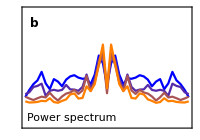

```mathematica
(* normalised power spectrum plot *)
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->{-0.2,1},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Range[0,1,0.2]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAC,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

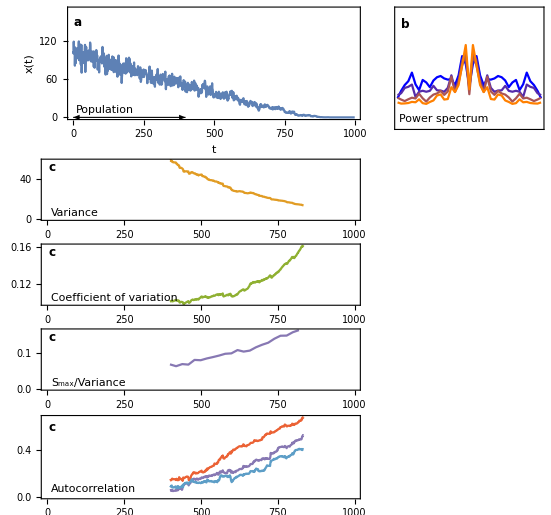

```mathematica
plotGrid
```

```mathematica
Export["figures/single_"<>simName<>".png",plotGrid,ImageResolution->200];
```